Zadání úkolu:

-Graphics-

1. Obvod na obrázku popište obvodovými rovnicemi.
2. Přepište popis obvodu do SW Mathematica a vyřešte tento obvod pro tyto hodnoty součástek:R1=10 kΩ,R2=22 kΩ,R3=33 kΩ,C1=56 nF,C2=47 nF.L1=82 μH.L2=56 μH.
3. Vstupní napětí uz[t]=amplitudaU*(Sin[2*Pi*frekvenceU*t])/2,kde amplitudaU=5 V a frekvenceU=1200 Hz.
4. Vstupní proud iz[t]=amplitudaI*(Sin[2*Pi*frekvenceI*t])/2,kde amplitudaI=100 mA a frekvenceI=2400 Hz.
5. Vykreslete průběh napětí uout(t),pro průběh napětí použijte modrou barvu.
6. Překreslete obvod pro stejnosměrný stav a vyřešte jej pro hodnotu stejnosměrného napětí Uz=5 V a stejnosměrného proudu Iz=100 mA.


Poznámka 1:Tento obvod nelze řešit přímo pomocí NDSolve,protože kondenzátor C2 je připojen přímo na svorky zdroje napětí.Aby bylo možno obvod vyřešit,doporučujeme sériově s kondenzátorem C2 zařadit malý odpor Rx.Pro prvotní řešení nastavte hodnotu Rx relativně velkou (např.Rx=1000) a poté ji postupne snižujte (až k hodnotě 0,1 a případně i méně),dokud bude ještě možné obdvod řešit.Řešení,které obdržíte,bude mít jenom malou odchylkou od skutečnosti.

Poznámka 2:V Mathematice v10 a v11 je možno řešit i bez přidaného odporu Rx. Stačí v NDSolve přidat další nepovinný parametr Method→{"IndexReduction"→True}.

Poznámka 3:Počítá se i snaha příklad řešit.

Varování:Parametry součástek nekopírujte z textu,nakopírují se i nepoužitelné znaky!

Řešení úkolu:

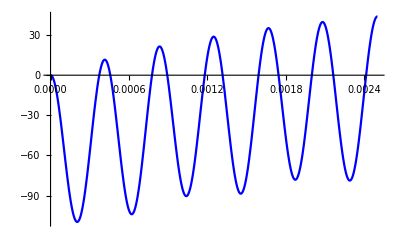

```mathematica
ClearAll["Global`*"]

uzel1=0==iC1[t]+iR1[t]+iL1[t];
uzel2=iC1[t]==iR3[t]+iZ[t];
uzel3=iR1[t]+iL1[t]==iR2[t]+iU[t]+iC2[t];
uzel4=iR3[t]+iR2[t]==iL2[t];

ZdrojU=uZ[t]==u3[t];
RezR1=u1[t]-u3[t]==iR1[t]*R1;
RezR2=u3[t]-u4[t]==iR2[t]*R2;
RezR3=u2[t]-u4[t]==iR3[t]*R3;
CivL1=u1[t]-u3[t]==iL1'[t]*L1;
CivL2=u4[t]==iL2'[t]*L2;
KonC1=iC1[t]==(u1'[t]-u2'[t])*C1;
KonC2=iC2[t]==u3'[t]*C2;

poc1=iL1[0]==0;
poc2=iL2[0]==0;
poc3=u1[0]==0;
poc4=u2[0]==0;
poc5=u3[0]==0;

rovnice={uzel1,uzel2,uzel3,uzel4,ZdrojU,RezR1,RezR2,RezR3,CivL1,CivL2,KonC1,KonC2,poc1,poc2,poc3,poc4,poc5};

amplitudaU=5;
frekvenceU=1200;
perioda=1/frekvenceU;

amplitudaI=100*10^-3;
frekvenceI=2400;

tmax=3*perioda;

soucastky={R1->10*10^3,R2->22*10^3,R3->33*10^3,
C1->56*10^-9,C2->47*10^-9,
L1->82*10^-6,L2->56*10^-6,
uZ[t]->amplitudaU*(Sin[2*Pi*frekvenceU*t])/2,
iZ[t]->amplitudaI*(Sin[2*Pi*frekvenceI*t])/2};

nezname={u1[t],u2[t],u3[t],u4[t],iU[t],iR1[t],iR2[t],iR3[t],iL1[t],iL2[t],iC1[t],iC2[t]};

reseni=NDSolve[rovnice/.soucastky,nezname,{t,0,tmax},Method->{"IndexReduction"->True},StartingStepSize->10^-9];
Plot[Evaluate[u2[t]/.reseni], {t,0,tmax}, PlotRange->All, PlotStyle->Blue]
```